```mathematica
Quit[]
```

## Tools FG

```mathematica
(*cl[d_,l_]:=(Sqrt[π]Gamma[l+1]Gamma[(d-2)/2])/(2^(l+1) Gamma[l+(d-1)/2]);(*some other normalization term*)(*d-dim Partial Wave integrand {t,4,∞}*)*)
```

```mathematica
Clear[PolQ, PolQDer, z0t,z0u,tt,uu,discZ];
PolQ[J_, d_, z_]:=(4/Pi)(Sqrt[Pi]Gamma[J+1]Gamma[(d-2)/2])/(2^(J+1)Gamma[J+(d-1)/2] z^(J+1))Hypergeometric2F1[(J+1)/2,(J+2)/2, J+(d-1)/2,1/z^2];
PolQDer[J_,d_,z_]:=(D[PolQ[J,d,zz],{zz,1}]/.zz->z);
z0t[s_]:= (s+4)/(s-4);
z0u[s_]:= (s+4)/(4-s);
tt[s_,z_]:=((4-s)/2) (1-z);
uu[s_,z_]:=((4-s)/2 )(1+z);
discZ[expr_,s_,z_,eps_:10^-12]:= (expr[Re[s],z+eps I]-expr[Re[s],z-eps I])/(2I)
```

```mathematica
Clear[iQInfinity12,tail]
iQInfinity12[start_, J_, d_]=Integrate[PolQ[J,d,z] 1/z^(1/2), {z, start, Infinity}, GenerateConditions->False]
tail[amplitudeT_, s_, J_, d_, start_]:= Module[{zvals, yvals, coeff12},
								zvals = Abs[start[s]]*{100000,1000000, 10000000};
								yvals=amplitudeT[s,#]&/@zvals;
								coeff12=Mean[yvals*zvals^(1/2)];
								iQInfinity12[50000Abs[start[s]], J, d]coeff12]
```

1/(√π)2^-J (1/start^2)^(1/4+J/2) Gamma[-1+d/2] Gamma[1/4+J/2] Gamma[1+J] HypergeometricPFQRegularized[{1/4 (1+2 J),(1+J)/2,(2+J)/2},{1/4 (5+2 J),1/2 (-1+d)+J},1/start^2]

```mathematica
Clear[MyNIntegrateFaster];
MyNIntegrateFaster[expr_,{x_,a_,b_},p_]:=Module[{temp=expr},(*Print["integrate..."];*)temp=SetPrecision[temp,8*p];
temp=NIntegrate[temp,{x,a,b},Method->"GaussKronrodRule",WorkingPrecision->4*p,PrecisionGoal->p,AccuracyGoal->p,MaxRecursion->100];
temp=SetPrecision[temp,p];
Return[temp];];
```

```mathematica
Clear[t,u, rho, rhoT,rhoZ]
rho[s_,sigma_:20/3]:=(Sqrt[sigma-4]-Sqrt[4-s])/(Sqrt[sigma-4]+Sqrt[4-s])
rhoZ[s_,z_]:=rho[tt[s,z]];
(*Discontinuity of the rho wavelet*)
rhoT[t_,sigma_:20/3]:=(2 Sqrt[t-4] Sqrt[sigma-4])/(t+sigma-8)
```

## Comparison Froissart Gribov and usual projection for rho ansatz s>4

```mathematica
d=4;
```

```mathematica
Clear[exprSTU,expr,DiscExpr]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExpr[s_,z_]:=rhoT[tt[s,z]]
```

```mathematica
Clear[exprJmain,exprJtail,exprJ]
p0=8;
exprJmain[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z](*exprInt[z]*)DiscExpr[s,z],{z, z0t[s],(*50000 z0[s]*)Infinity},p0];
exprJtail[J_,s_]=tail[DiscExpr, s, J, d,z0t];
exprJ[J_,s_]:=exprJmain[J,s]+exprJtail[J,s];
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
data4ds5to95=ParallelTable[{J,Abs[(exprJmain[J,s+10^-16 I]-IPt[J,s+10^-16 I])/(exprJmain[J,s+10^-16 I]+IPt[J,s+10^-16 I])]},{s,5,95,10},{J,2,12,2}]
```

{{{2,2.×10^-7},{4,1.3×10^-6},{6,2.×10^-6},{8,2.9×10^-6},{10,3.84×10^-6},{12,4.92×10^-6}},{{2,0.},{4,0.},{6,4.58×10^-6},{8,0.00005191},{10,0.0000686},{12,0.00008669}},{{2,0.},{4,0.},{6,0.},{8,4.39×10^-6},{10,0.00004617},{12,0.0001647}},{{2,0.},{4,0.},{6,0.},{8,2.3×10^-6},{10,8.37×10^-6},{12,0.0000296}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,3.85×10^-6},{12,0.0000136}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,5.87×10^-6}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,6.93×10^-6}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}},{{2,0.},{4,0.},{6,0.},{8,0.},{10,0.},{12,0.}}}

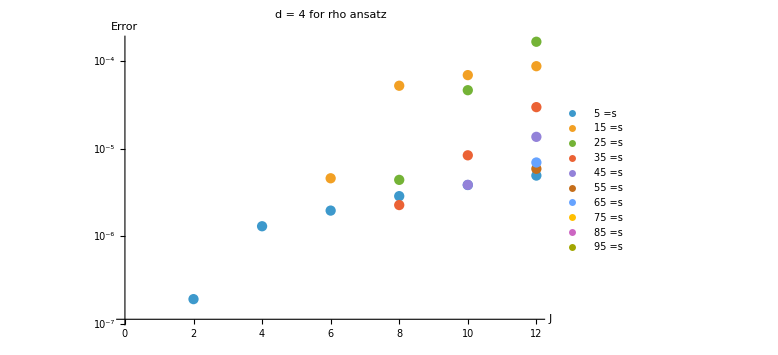

```mathematica
ListLogPlot[data4ds5to95,PlotLabel->Style["d = 4 for rho ansatz",16,Bold],AxesLabel->{Style["J",14],Style["Error",14]},PlotLegends->"=s"Range[5,95,10],ImageSize->Large]
```

## Comparison Froissart Gribov and usual projection for rho ansatz s<4

```mathematica
Clear[exprSTU,expr,DiscExpr]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExpr[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[exprJmain,exprJtail,exprJ]
p0=8;
exprJmain[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z](*exprInt[z]*)DiscExpr[s,z],{z, z0u[s],(*50000 Abs[z0u[s]]*)Infinity},p0];
(*exprJtail[J_,s_]=iQInfinity12[50000 Abs[z0u[s]], J, d](Series[DiscExpr[-10+10^-10 I,z],{z,Infinity,1}]Sqrt[z]//Normal)/.z->1;
exprJ[J_,s_]:=exprJmain[J,s]+exprJtail[J,s];*)
```

```mathematica
MyNIntegrateFaster[PolQ[6,d,z](*exprInt[z]*)DiscExpr[-10-10^-10 I,z],{z, z0u[-10-10^-10 I],(*50000 z0[s]*)1},p0]
MyNIntegrateFaster[PolQ[6,d,z](*exprInt[z]*)DiscExpr[-10+10^-10 I,z],{z, z0u[-10+10^-10 I],(*50000 z0[s]*)1},p0]
exprJmain[6,-10+10^-10 I]
IPt[6,-10+10^-10 I]
```

0.04223488-0.053347348 ⅈ

0.04223488+0.053347348 ⅈ

0.066715075+0.05334734 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.06671507707308969+0.053347347900037 ⅈ

```mathematica
data4dsmin10to2=ParallelTable[{J,Quiet[Abs[(exprJmain[J,s-10^-16 I]-IPt[J,s-10^-16 I])/(exprJmain[J,s-10^-16 I]+IPt[J,s-10^-16 I])]]},{s,-10,2,2},{J,2,12,2}];
```

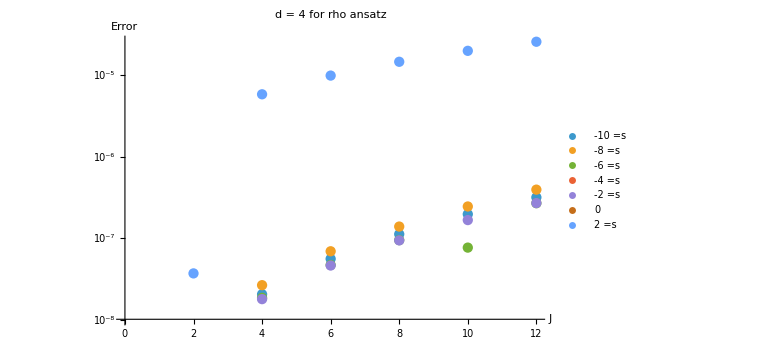

```mathematica
ListLogPlot[data4dsmin10to2,PlotLabel->Style["d = 4 for rho ansatz",16,Bold],AxesLabel->{Style["J",14],Style["Error",14]},PlotLegends->"=s"Range[-10,2,2],ImageSize->Large]
```

## Computation rho ansatz deep s

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=rhoT[tt[s,z]]
DiscExprU[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[exprJmain1,exprJmain2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z]DiscExprT[s,z],{z, z0t[s],Infinity},p0];
exprJmain2[J_,s_]:=MyNIntegrateFaster[PolQ[J,d,z]DiscExprU[s,z],{z, z0u[s],Infinity},p0];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s],exprJmain2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
exprJ[2,-10-9I ]-IPt[2,-10-9I ]
```

0.+0. ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Following the cuts

```mathematica
z1[s_,t_]:=1+(2t)/(s-4);
```

```mathematica
b0 = Table[z1[4+Exp[I Pi theta],t],{theta,0,1,0.1},{t,4,100,0.1}];(*
a0 = Table[z0t[4+Exp[2I Pi theta+I 0.01]]+t Exp[I Arg[z0t[4+Exp[2I Pi theta]]-1]],{theta,0,1,0.1},{t,0,100,1}];*)
```

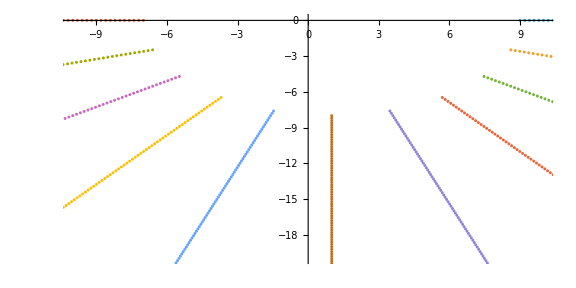

```mathematica
Show[ComplexListPlot[b0, ImageSize->Large, PlotRange->{-20-20I,20+0.1I}, AspectRatio->1/2](*,ComplexListPlot[a0, ImageSize->Large, PlotRange->{-10-20I,10+20I}, AspectRatio->1]*)]
```

## Computation rho ansatz deep s domain int compactified

The relatively low precision of half infinite domain and the hardship of looking at the tail on an angled branch cut means compactifying the integral might be the most effective pass.

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=rho[s]+rho[t]+rho[u];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=rhoT[tt[s,z]]
DiscExprU[s_,z_]:=rhoT[uu[s,z]]
```

```mathematica
Clear[HalfCompactify,CompactIntegrand]
HalfCompactify[s0_,ϕ_]:=(2 s0)/(1+Cos[ϕ]);
CompactIntegrand[x_,var_,s0_]:=D[HalfCompactify[s0,ϕ],ϕ] (x/.var->HalfCompactify[s0,ϕ]);
```

```mathematica
Clear[exprJmain1,exprJmain2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprT[s,z])//CompactIntegrand[#,z,z0t[s]]&,{ϕ,0,π},p0];
exprJmain2[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprU[s,z])//CompactIntegrand[#,z,z0u[s]]&,{ϕ,0,π},p0];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s],exprJmain2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},p0]
```

```mathematica
exprJ[2,-10-9I ]-IPt[2,-10-9I ]
```

0.+0. ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Computation divergent threshold (n half integer) deep s domain int compactified d=6

```mathematica
d=6;
n=1;
div[s_]:=(4-s)^(-n-1/2)
divT[s_]:=(-1)^n(s-4)^(-n-1/2)
```

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=div[s]+div[u]+div[t];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
DiscExprT[s_,z_]:=divT[tt[s,z]]
DiscExprU[s_,z_]:=divT[uu[s,z]]
```

```mathematica
Clear[epsilonT,epsilonU]
epsilonT[J_,s_]=(*Abs[PolQ[J, d, z0t[s]]/PolQDer[J,d,z0t[s],1]]*)10^-5//Simplify;
epsilonU[J_,s_]=(*Abs[PolQ[J, d, z0u[s]]/PolQDer[J,d,z0u[s],1]]*)10^-5//Simplify;
```

Might be optimized by precomputing the derivatives to the Legendre Q function.

```mathematica
Clear[HalfCompactify,CompactIntegrand]
HalfCompactify[s0_,ϕ_]:=(2 s0)/(1+Cos[ϕ]);
CompactIntegrand[x_,var_,s0_]:=D[HalfCompactify[s0,ϕ],ϕ] (x/.var->HalfCompactify[s0,ϕ]);
```

```mathematica
Clear[exprJmain1,exprJmain2,exprJkeyhole1,exprJkeyhole2]
p0=8;
exprJmain1[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprT[s,z])//CompactIntegrand[#,z,z0t[s]+Exp[I Arg[-1+z0t[s]]]epsilonT[J,s]]&,{ϕ,0,π},p0];
exprJkeyhole1[J_, s_, ord_: 4] := Module[
  {z0, dir, eps, α, c0, qk},
  z0  = z0t[s];
  dir = Exp[I Arg[z0 - 1]];   (* direction of the cut / keyhole ray *)
  eps = epsilonT[J, s];
  α   = n + 1/2;
  (* regular prefactor of the discontinuity at the branch point *)
  c0 = Limit[
    (z - z0)^α DiscExprT[s, z],
    z -> z0,
    Direction -> dir
  ];
  qk[k_] := SeriesCoefficient[PolQ[J, d, z], {z, z0, k}];
  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
];
exprJmain2[J_,s_]:=MyNIntegrateFaster[(PolQ[J,d,z]DiscExprU[s,z])//CompactIntegrand[#,z,z0u[s]+Exp[I Arg[1+z0u[s]]]epsilonU[J,s]]&,{ϕ,0,π},p0];
exprJkeyhole2[J_, s_, ord_: 4] := Module[
  {z0, dir, eps, α, c0, qk},
  z0  = z0u[s];
  dir = Exp[I Arg[z0 + 1]];   (* direction of the cut / keyhole ray *)
  eps = epsilonT[J, s];
  α   = n + 1/2;
  (* regular prefactor of the discontinuity at the branch point *)
  c0 = Limit[
    (z - z0)^α DiscExprT[s, z],
    z -> z0,
    Direction -> dir
  ];
  qk[k_] := SeriesCoefficient[PolQ[J, d, z], {z, z0, k}];
  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
];
exprJ[J_,s_]:=If[Re[s]>4,exprJmain1[J,s]+exprJkeyhole1[J,s],exprJmain2[J,s]+exprJkeyhole2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
JJ=2;
ss=9+ 0.001I;
(exprJ[JJ,ss ]-IPt[JJ,ss  ])/(exprJ[JJ,ss ]+IPt[JJ,ss  ])
exprJ[JJ,ss ]
IPt[JJ,ss  ]
```

3.47874×10^-11-1.07628×10^-13 ⅈ

0.00292571+4.87619×10^-7 ⅈ

0.002925714331767196+4.87619046144×10^-7 ⅈ

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,0.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Computation divergent threshold (n integer deep s domain int compactified d=6

```mathematica
d=6;
n=1;
div[s_]:=(4-s)^-n
```

```mathematica
Clear[exprSTU,expr,DiscExprT,DiscExprU]
exprSTU[s_,t_,u_]:=div[s]+div[u]+div[t];
expr[s_,z_]:=exprSTU[s, tt[s,z],uu[s,z]];
```

```mathematica
Clear[exprJmain1,exprJmain2,exprJthresh1,exprJthresh2]
exprJthresh1[J_,s_]:=(Pi (-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0t[s])((s-4)/2)^-n;
exprJthresh2[J_,s_]:=(Pi(-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0u[s])((4-s)/2)^-n;
exprJ[J_,s_]:=If[Re[s]>4,exprJthresh1[J,s],exprJthresh2[J,s]]
```

```mathematica
Pgen[J_,d_,z_]:=(*GegenbauerC[J,(d-3)/2,z]/GegenbauerC[J,(d-3)/2,1]*)Hypergeometric2F1[-l,l+d-3,(d-2)/2,(1-x)/2]/.l->J/.x->z;
IPt[J_,s_]:=MyNIntegrateFaster[Sin[θ]*(1-Cos[θ]^2)^((d-4)/2)Pgen[J,d,Cos[θ]]*expr[s,Cos[θ]],{θ,0,Pi},16]
```

```mathematica
N[exprJthresh1[20,-10-10I]]
IPt[20,-10-10I ]
```

-2.26966×10^-6+9.13908×10^-6 ⅈ

-2.26965846306778×10^-6+9.139078603778756×10^-6 ⅈ

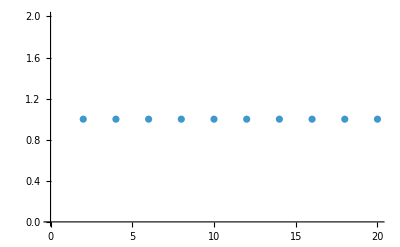

```mathematica
ListPlot[Table[{J,(Abs[N[exprJ[J,10]]/IPt[J,10 ]])},{J,2,20,2}]]
```

```mathematica
Timing[data=ParallelTable[{xx, y,Quiet[Abs[(exprJ[J,xx+I y]-IPt[J,xx+I y])/(exprJ[J,xx+I y]+IPt[J,xx+I y])]]},{J,2,12,2},{xx,-10.1,10.1,1},{y,-10.1,10.1,1}]]
```

```mathematica
data/.{a_,b_,c_}->c
```

## Full divergent part part

```mathematica
Clear[exprJkeyhole,exprJthresh]
exprJkeyhole[J_,s_,n_]:=Module[{div,divT,exprSTU,expr,DiscExprT,exprJmain,exprJkeyhole1},
div[ss_]:=(4-ss)^-n;
divT[ss_]:=(-1)^n(ss-4)^-n;
exprSTU[ss_,t_,u_]:=div[ss]+div[u]+div[t];
expr[ss_,z_]:=exprSTU[ss, tt[ss,z],uu[ss,z]];
DiscExprT[ss_,z_]:=divT[tt[ss,z]];
exprJmain[JJ_,ss_]:=MyNIntegrateFaster[(PolQ[JJ,d,z]DiscExprT[ss,z])//CompactIntegrand[#,z,z0t[ss]+Exp[I Arg[-1+z0t[ss]]]epsilonT[JJ,ss]]&,{ϕ,0,π},p0];
exprJkeyhole1[JJ_, ss_, ord_: 4] := Module[
	  {z0, dir, eps, α, c0, qk},
	  z0  = z0t[ss];
	  dir = Exp[I Arg[z0 - 1]];   (* direction of the cut / keyhole ray *)
	  eps = 10^-5;
	  α   = n ;
	  (* regular prefactor of the discontinuity at the branch point *)
	  c0 = Limit[(z - z0)^α DiscExprT[ss, z],z -> z0,Direction -> dir];
	  qk[k_] := SeriesCoefficient[PolQ[JJ, d, z], {z, z0, k}];
	  c0*Sum[qk[k]*dir^(k+1- α)*eps^(k + 1 - α)/(k + 1 - α),{k, 0, ord}]
	];
exprJmain[J,s]+exprJkeyhole1[J,s]
];
exprJthresh[J_,s_]:=Module[{Residue, Keyhole},
Residue=Sum[α[0,0,0,Boole[EvenQ[d]]-2(n-Floor[(d-3)/2])](Pi (-1)^(n+1))/((n-1)!)(D[PolQ[J,d,z],{z,n-1}]/.z->z0t[s])((s-4)/2)^-n,{n,Floor[(d-3)/2],1,-1}];
Keyhole=Sum[α[0,0,0,Boole[OddQ[d]]-2(n-Floor[(d-4)/2]-1/2)]exprJkeyhole[J,s,n],{n,Floor[(d-4)/2]+1/2,1/2,-1}];
Residue+Keyhole/.mysdpbout[[2]]
];
```

```mathematica
exprJthresh[3,10+I]
```

0.0035709538+0.0038488178 ⅈ